```mathematica
hbarc = 0.197326938;
outputDir = "/Users/derek/github/freestream-cartesian/output";
```

```mathematica
initEnergyDensity = Import[outputDir<>"/initial_e.dat", "TSV"];
initBaryonDensity = Import[outputDir<>"/initial_nB.dat", "TSV"];
streamedEnergyDensity = Import[outputDir<>"/e.dat", "TSV"];
streamedBaryonDensity = Import[outputDir<>"/nB.dat", "TSV"];
streamedPressure = Import[outputDir<>"/p.dat", "TSV"];
streamedBulkPressure = Import[outputDir<>"/bulk_PI.dat", "TSV"];
flowVelocityX =  Import[outputDir<>"/u_x.dat", "TSV"];
flowVelocityY =  Import[outputDir<>"/u_y.dat", "TSV"];
baryonDiffusionX = Import[outputDir<>"/V_x.dat", "TSV"];
baryonDiffusionY = Import[outputDir<>"/V_y.dat", "TSV"];

initEnergyDensityTable=Table[StringReplace[ToString[initEnergyDensity[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@initEnergyDensity}];
initBaryonDensityTable=Table[StringReplace[ToString[initBaryonDensity[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@initBaryonDensity}];
streamedEnergyDensityTable=Table[StringReplace[ToString[streamedEnergyDensity[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@streamedEnergyDensity}];
streamedBaryonDensityTable=Table[StringReplace[ToString[streamedBaryonDensity[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@streamedBaryonDensity}];
streamedPressureTable=Table[StringReplace[ToString[streamedPressure[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@streamedPressure}];
streamedBulkPressureTable=Table[StringReplace[ToString[streamedBulkPressure[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@streamedBulkPressure}];
flowVelocityXTable = Table[StringReplace[ToString[flowVelocityX[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@flowVelocityX}];
flowVelocityYTable = Table[StringReplace[ToString[flowVelocityY[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@flowVelocityY}];

initEnergyDensityInterp = Interpolation[initEnergyDensityTable, InterpolationOrder->3];
initBaryonDensityInterp = Interpolation[initBaryonDensityTable, InterpolationOrder->3];
streamedEnergyDensityInterp = Interpolation[streamedEnergyDensityTable, InterpolationOrder->3];
streamedBaryonDensityInterp = Interpolation[streamedBaryonDensityTable, InterpolationOrder->3];
streamedPressureInterp = Interpolation[streamedPressureTable, InterpolationOrder->3];
streamedBulkPressureInterp = Interpolation[streamedBulkPressureTable, InterpolationOrder->3];
flowVelocityXInterp = Interpolation[flowVelocityXTable, InterpolationOrder->3];
flowVelocityYInterp = Interpolation[flowVelocityYTable, InterpolationOrder->3];
```

```mathematica
xlim = 2.5;
ylim = 2.5;
zlim = 2.5;
```

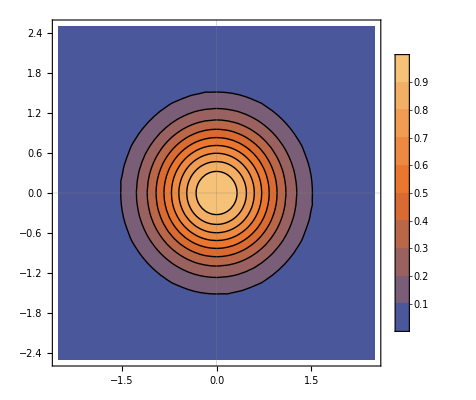

```mathematica
ContourPlot[initEnergyDensityInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

```mathematica
ContourPlot[initBaryonDensityInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

-Graphics-

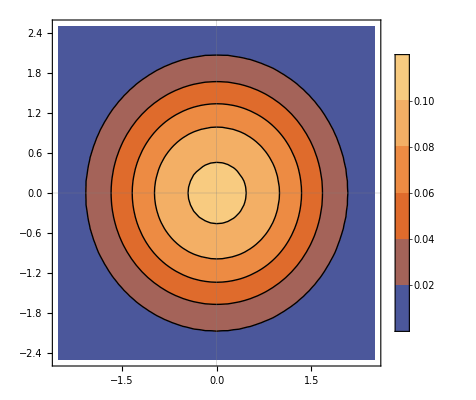

```mathematica
ContourPlot[streamedEnergyDensityInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

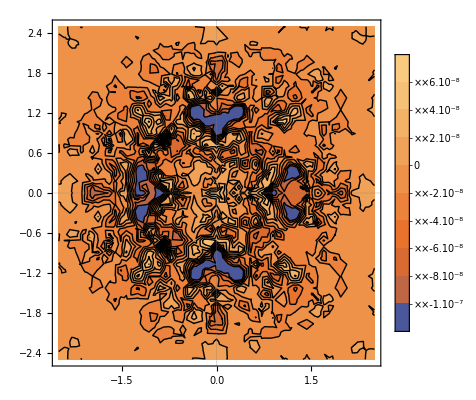

```mathematica
ContourPlot[streamedBulkPressureInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

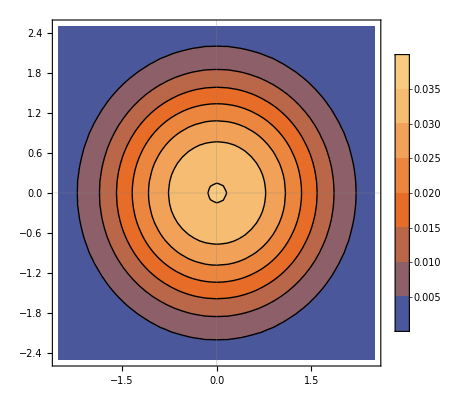

```mathematica
ContourPlot[streamedPressureInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

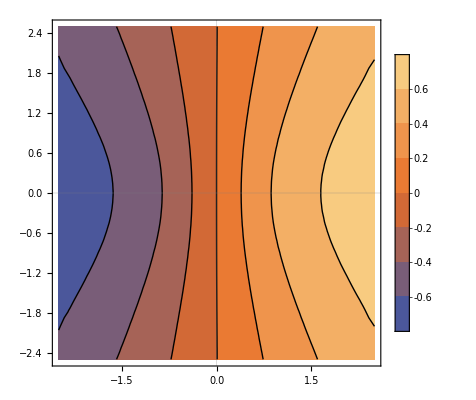

```mathematica
ContourPlot[flowVelocityXInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

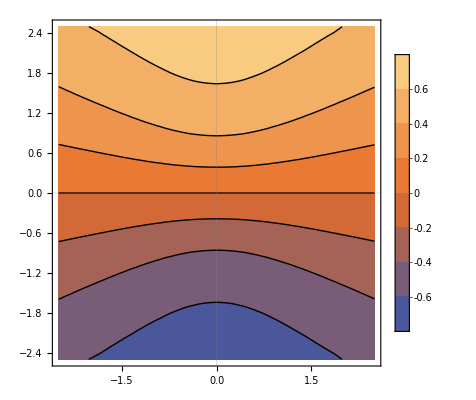

```mathematica
ContourPlot[flowVelocityYInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```